```mathematica
ClearAll["Global`*"]
```

```mathematica
J[ω_]:= (ω/ω1)^s;
Occ[ω_]:= (Exp[ω/kBT]-1)^-1;
SubPlus[λ] = ω1+ 2V;
SubMinus[λ] = ω1- 2V;
P = (1+Exp[δω/kBT2])((Occ[SubPlus[λ]+δω]J[SubPlus[λ]+δω]+Occ[SubMinus[λ]+δω]J[SubMinus[λ]+δω])/((Occ[SubMinus[λ]+δω]+1)J[SubMinus[λ]+δω]+(Occ[SubMinus[λ]]+1)J[SubMinus[λ]]));
```

```mathematica
Simplify[ D[Series[P, {δω,0,1}],δω]]
```

(ⅇ^(-ω1/kBT) (-ⅇ^((2 V)/kBT)+ⅇ^(ω1/kBT)) (1-(2 V)/ω1)^-s (-(ⅇ^((-2 V+ω1)/kBT) (1-(2 V)/ω1)^s)/((-1+ⅇ^((-2 V+ω1)/kBT))^2 kBT)-(ⅇ^((2 V+ω1)/kBT) (1+(2 V)/ω1)^s)/((-1+ⅇ^((2 V+ω1)/kBT))^2 kBT)+(s (1-(2 V)/ω1)^(-1+s))/((-1+ⅇ^((-2 V+ω1)/kBT)) ω1)+(s (1+(2 V)/ω1)^(-1+s))/((-1+ⅇ^((2 V+ω1)/kBT)) ω1))+1/(2 kBT kBT2 (-2 V+ω1))ⅇ^(-ω1/kBT) ((1-(2 V)/ω1)^s/(-1+ⅇ^((-2 V+ω1)/kBT))+(1+(2 V)/ω1)^s/(-1+ⅇ^((2 V+ω1)/kBT))) (1-(2 V)/ω1)^-s (ⅇ^(ω1/kBT) kBT (-kBT2 s-2 V+ω1)+ⅇ^((2 V)/kBT) (kBT (kBT2 s+2 V-ω1)+kBT2 (-2 V+ω1))))+O[δω]^1

Now I make an approximation: V/kBT=0

```mathematica
M = Simplify[(ⅇ^(-ω1/kBT) (-2  ω1+ⅇ^(ω1/kBT) (-2 V+ω1)+ⅇ^(ω1/kBT) (2 V+ω1)) (ⅇ^(ω1/kBT) kBT (-kBT2-2 V+ω1)+ (kBT (kBT2+2 V-ω1)+kBT2 (-2 V+ω1))))/(2 (-1+ⅇ^(ω1/kBT)) (-1+ⅇ^(ω1/kBT)) kBT kBT2 (-2 V+ω1)^2)+((1-ⅇ^(-ω1/kBT)) ω1 ((1/(-1+ⅇ^(ω1/kBT))-(ⅇ^(ω1/kBT) (-2 V+ω1))/((-1+ⅇ^(ω1/kBT))^2 kBT))/ω1+((-1+ⅇ^(ω1/kBT)) kBT-ⅇ^(ω1/kBT) (2 V+ω1))/((-1+ⅇ^(ω1/kBT))^2 kBT ω1)))/(-2 V+ω1)]
```

(ⅇ^(-ω1/kBT) (-(-1+2 ⅇ^(ω1/kBT)) kBT2 ω1 (-2 V+ω1)+(-1+ⅇ^(ω1/kBT)) kBT (kBT2 (-4 V+ω1)+ω1 (-2 V+ω1))))/((-1+ⅇ^(ω1/kBT)) kBT kBT2 (-2 V+ω1)^2)

```mathematica
ω1 = 8000.;V = 200.;kBT2 = 70.;kBT  = 6000.;
```

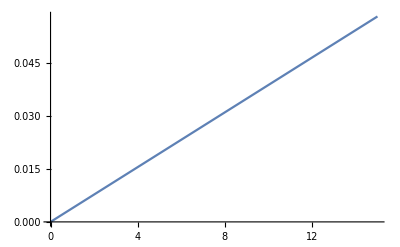

```mathematica
ListLinePlot[Table[{n, M n},{n,0,15, 0.1}]]
```

#### So we can see that the gradient is small and positive for increasing δω. This is different from the monomer case

```mathematica
M2 = Series[(ⅇ^(-ω1/kBT) (-1+ⅇ^(ω1/kBT)) (1-δ)^-s (-(ⅇ^(ω1/kBT) (1-δ)^s)/((-1+ⅇ^(ω1/kBT))^2 kBT)-(ⅇ^(ω1/kBT) (1+δ)^s)/((-1+ⅇ^(ω1/kBT))^2 kBT)+(s (1-δ)^(-1+s))/((-1+ⅇ^(ω1/kBT)) ω1)+(s (1+δ)^(-1+s))/((-1+ⅇ^(ω1/kBT)) ω1))+1/(2 kBT kBT2 (-2 V+ω1))ⅇ^(-ω1/kBT) ((1-δ)^s/(-1+ⅇ^(ω1/kBT))+(1+δ)^s/(-1+ⅇ^(ω1/kBT))) (1-δ)^-s (ⅇ^(ω1/kBT) kBT (-kBT2 s-2 V+ω1)+ (kBT (kBT2 s+2 V-ω1)+kBT2 (-2 V+ω1)))), {δ, 0,1}]
```

((2 ⅇ^(-ω1/kBT) (-kBT s+ⅇ^(ω1/kBT) kBT s-ⅇ^(ω1/kBT) ω1))/((-1+ⅇ^(ω1/kBT)) kBT ω1)+(ⅇ^(-ω1/kBT) (kBT (kBT2 s+2 V-ω1)+kBT2 (-2 V+ω1)+ⅇ^(ω1/kBT) kBT (-kBT2 s-2 V+ω1)))/((-1+ⅇ^(ω1/kBT)) kBT kBT2 (-2 V+ω1)))+((2 ⅇ^(-ω1/kBT) s (-kBT s+ⅇ^(ω1/kBT) kBT s-ⅇ^(ω1/kBT) ω1))/((-1+ⅇ^(ω1/kBT)) kBT ω1)+(ⅇ^(-ω1/kBT) s (kBT (kBT2 s+2 V-ω1)+kBT2 (-2 V+ω1)+ⅇ^(ω1/kBT) kBT (-kBT2 s-2 V+ω1)))/((-1+ⅇ^(ω1/kBT)) kBT kBT2 (-2 V+ω1))) δ+O[δ]^2

```mathematica
Solve[M2==0, s]
```

{{s→-((-kBT+ⅇ^(ω1/kBT) kBT+kBT2-2 ⅇ^(ω1/kBT) kBT2) ω1 (-2 V+ω1))/((-1+ⅇ^(ω1/kBT)) kBT kBT2 (-4 V+ω1))}}

```mathematica
sff[kBT_, kBT2_, ω1_,V_]:=-((-kBT+ⅇ^(ω1/kBT) kBT+kBT2-2 ⅇ^(ω1/kBT) kBT2) ω1 (-2 V+ω1))/((-1+ⅇ^(ω1/kBT)) kBT kBT2 (-4 V+ω1))
```

```mathematica
sff[6000., 300., 8000.,200.]
```

-24.8295

```mathematica
Subscript[A, Bs]= Subscript[Γ, GBs]/(Subscript[Γ, BsB]+Subscript[Γ, BsDs] +Subscript[Γ, BsD]);
```

```mathematica
Subscript[A, Bs]= 0;
```

```mathematica
Subscript[Γ, GB]
```

Γ_GB

```mathematica
Subscript[A, B]= (Subscript[Γ, GB]+Subscript[Γ, BsB] 0)/(Subscript[Γ, BG] +Subscript[Γ, BGs]+Subscript[Γ, BDs] +Subscript[Γ, BD])
```

Γ_GB/(Γ_BD+Γ_BDs+Γ_BG+Γ_BGs)

```mathematica
Subscript[A, D]=(Subscript[Γ, GsG]- Subscript[Γ, BGs] Subscript[A, B])/Subscript[Γ, DGs]
```

(-(Γ_BGs Γ_GB)/(Γ_BD+Γ_BDs+Γ_BG+Γ_BGs)+Γ_GsG)/Γ_DGs

```mathematica
Subscript[A, Ds]= ((Subscript[Γ, DDs]+ Subscript[Γ, DGs])Subscript[A, D]- Subscript[Γ, BD] Subscript[A, B])/Subscript[Γ, DsD]
```

(-(Γ_BD Γ_GB)/(Γ_BD+Γ_BDs+Γ_BG+Γ_BGs)+((Γ_DDs+Γ_DGs) (-(Γ_BGs Γ_GB)/(Γ_BD+Γ_BDs+Γ_BG+Γ_BGs)+Γ_GsG))/Γ_DGs)/Γ_DsD

```mathematica
Subscript[A, Gs]= ((Subscript[Γ, GBs] +Subscript[Γ, GB]+Subscript[Γ, GDs] +Subscript[Γ, BG])-(Subscript[Γ, BG] Subscript[A, B]))/Subscript[Γ, GsG]
```

(Γ_BG+Γ_GB-(Γ_BG Γ_GB)/(Γ_BD+Γ_BDs+Γ_BG+Γ_BGs)+Γ_GBs+Γ_GDs)/Γ_GsG

```mathematica
Subscript[A, Gs]= 0
```

0

```mathematica
P = Expand[(Subscript[A, D]+ Subscript[A, Ds])/1 ];
Ps3 =Simplify[P, {Subscript[Γ, BD]+Subscript[Γ, BDs]+Subscript[Γ, BG]+Subscript[Γ, BGs]=Subscript[Γ, BD]+Subscript[Γ, BDs]+Subscript[Γ, BGs]}]
```

```mathematica
(-Subscript[Γ, BGs] (Subscript[Γ, DDs]+Subscript[Γ, DGs]+Subscript[Γ, DsD]) (Subscript[Γ, GB]-Subscript[Γ, GsG])+(Subscript[Γ, BDs]+Subscript[Γ, BG]) (Subscript[Γ, DDs]+Subscript[Γ, DGs]+Subscript[Γ, DsD]) Subscript[Γ, GsG]+Subscript[Γ, BD] ((Subscript[Γ, DDs]+Subscript[Γ, DsD]) Subscript[Γ, GsG]+Subscript[Γ, DGs] (-Subscript[Γ, GB]+Subscript[Γ, GsG])))/((Subscript[Γ, BD]+Subscript[Γ, BDs]+Subscript[Γ, BG]+Subscript[Γ, BGs]) Subscript[Γ, DGs] Subscript[Γ, DsD]);
Ps4 = Simplify[Expand[(-Subscript[Γ, BGs] (Subscript[Γ, DDs]+Subscript[Γ, DGs]+Subscript[Γ, DsD]) (Subscript[Γ, GB]-Subscript[Γ, GsG])+(Subscript[Γ, BDs]+Subscript[Γ, BG]) (Subscript[Γ, DDs]+Subscript[Γ, DGs]+Subscript[Γ, DsD]) Subscript[Γ, GsG]+Subscript[Γ, BD] ((Subscript[Γ, DDs]+Subscript[Γ, DsD]) Subscript[Γ, GsG]+Subscript[Γ, DGs] (Subscript[Γ, GsG])))/((Subscript[Γ, BD]+Subscript[Γ, BDs]+Subscript[Γ, BGs]) Subscript[Γ, DGs] Subscript[Γ, DsD])]]
```

((Γ_DDs+Γ_DGs+Γ_DsD) ((Γ_BD+Γ_BDs+Γ_BG) Γ_GsG+Γ_BGs (-Γ_GB+Γ_GsG)))/((Γ_BD+Γ_BDs+Γ_BGs) Γ_DGs Γ_DsD)

```mathematica
Ps5 =Expand[((Subscript[Γ, DDs]+Subscript[Γ, DsD]) ((Subscript[Γ, BD]+Subscript[Γ, BDs]) Subscript[Γ, GsG]+Subscript[Γ, BGs] (Subscript[Γ, GsG])))/((Subscript[Γ, BDs]+Subscript[Γ, BGs]) Subscript[Γ, DGs] Subscript[Γ, DsD])]
```

(Γ_BD Γ_GsG)/((Γ_BDs+Γ_BGs) Γ_DGs)+(Γ_BDs Γ_GsG)/((Γ_BDs+Γ_BGs) Γ_DGs)+(Γ_BGs Γ_GsG)/((Γ_BDs+Γ_BGs) Γ_DGs)+(Γ_BD Γ_DDs Γ_GsG)/((Γ_BDs+Γ_BGs) Γ_DGs Γ_DsD)+(Γ_BDs Γ_DDs Γ_GsG)/((Γ_BDs+Γ_BGs) Γ_DGs Γ_DsD)+(Γ_BGs Γ_DDs Γ_GsG)/((Γ_BDs+Γ_BGs) Γ_DGs Γ_DsD)

```mathematica
Occ[ω_, kBT_]:= (Exp[ω/kBT]-1)^-1
GammaUp[ω_, kBT_, Gamma_]:= Gamma Occ[ω, kBT]  ω/Subscript[ω, 13]
GammaDown[ω_, kBT_, Gamma_]:= Gamma [Occ[ω, kBT]+1]  ω/Subscript[ω, 13]
```

```mathematica
Subscript[Γ, BD] = GammaDown[Subscript[ω, B]
```

```mathematica
Expand[(Subscript[Γ, BDs]+Subscript[Γ, BGs]) Subscript[Γ, DGs]]
```

Γ_BDs Γ_DGs+Γ_BGs Γ_DGs

```mathematica
Ps = Expand[(Subscript[Γ, GsG] (-Subscript[Γ, BGs] (Subscript[Γ, DDs]+Subscript[Γ, DsD]) (Subscript[Γ, GsG])+(Subscript[Γ, BDs]) (Subscript[Γ, DDs]+Subscript[Γ, DsD]) Subscript[Γ, GsG]+Subscript[Γ, BD] ((Subscript[Γ, DDs]+Subscript[Γ, DsD]) Subscript[Γ, GsG]+Subscript[Γ, DGs] (Subscript[Γ, GsG]))))/(Subscript[Γ, DGs] Subscript[Γ, DsD] (Subscript[Γ, BG]^2+Subscript[Γ, BGs] Subscript[Γ, GB]+Subscript[Γ, BGs] Subscript[Γ, GBs]+Subscript[Γ, BGs] Subscript[Γ, GDs]+Subscript[Γ, BGs] Subscript[Γ, GsG]+Subscript[Γ, BG] (Subscript[Γ, BGs]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BD] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BDs] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])))]
```

(Γ_BD Γ_GsG^2)/(Γ_DGs (Γ_BG^2+Γ_BGs Γ_GB+Γ_BGs Γ_GBs+Γ_BGs Γ_GDs+Γ_BGs Γ_GsG+Γ_BG (Γ_BGs+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BD (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BDs (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)))+(Γ_BDs Γ_GsG^2)/(Γ_DGs (Γ_BG^2+Γ_BGs Γ_GB+Γ_BGs Γ_GBs+Γ_BGs Γ_GDs+Γ_BGs Γ_GsG+Γ_BG (Γ_BGs+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BD (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BDs (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)))-(Γ_BGs Γ_GsG^2)/(Γ_DGs (Γ_BG^2+Γ_BGs Γ_GB+Γ_BGs Γ_GBs+Γ_BGs Γ_GDs+Γ_BGs Γ_GsG+Γ_BG (Γ_BGs+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BD (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BDs (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)))+(Γ_BD Γ_GsG^2)/(Γ_DsD (Γ_BG^2+Γ_BGs Γ_GB+Γ_BGs Γ_GBs+Γ_BGs Γ_GDs+Γ_BGs Γ_GsG+Γ_BG (Γ_BGs+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BD (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BDs (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)))+(Γ_BD Γ_DDs Γ_GsG^2)/(Γ_DGs Γ_DsD (Γ_BG^2+Γ_BGs Γ_GB+Γ_BGs Γ_GBs+Γ_BGs Γ_GDs+Γ_BGs Γ_GsG+Γ_BG (Γ_BGs+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BD (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BDs (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)))+(Γ_BDs Γ_DDs Γ_GsG^2)/(Γ_DGs Γ_DsD (Γ_BG^2+Γ_BGs Γ_GB+Γ_BGs Γ_GBs+Γ_BGs Γ_GDs+Γ_BGs Γ_GsG+Γ_BG (Γ_BGs+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BD (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BDs (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)))-(Γ_BGs Γ_DDs Γ_GsG^2)/(Γ_DGs Γ_DsD (Γ_BG^2+Γ_BGs Γ_GB+Γ_BGs Γ_GBs+Γ_BGs Γ_GDs+Γ_BGs Γ_GsG+Γ_BG (Γ_BGs+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BD (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BDs (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)))

```mathematica
Ps2 = Simplify[Ps, (Subscript[Γ, DGs] (Subscript[Γ, BG]^2+Subscript[Γ, BGs] Subscript[Γ, GB]+Subscript[Γ, BGs] Subscript[Γ, GBs]+Subscript[Γ, BGs] Subscript[Γ, GDs]+Subscript[Γ, BGs] Subscript[Γ, GsG]+Subscript[Γ, BG] (Subscript[Γ, BGs]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BD] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BDs] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])))=Subscript[Γ, DGs] (Subscript[Γ, BGs] Subscript[Γ, GsG]+Subscript[Γ, BG] Subscript[Γ, GsG]+Subscript[Γ, BD] Subscript[Γ, GsG]+Subscript[Γ, BDs] Subscript[Γ, GsG]) ]
```

(((Γ_BDs-Γ_BGs) (Γ_DDs+Γ_DsD)+Γ_BD (Γ_DDs+Γ_DGs+Γ_DsD)) Γ_GsG^2)/(Γ_DGs Γ_DsD (Γ_BG^2+Γ_BG Γ_BGs+Γ_BGs Γ_GB+Γ_BG Γ_GBs+Γ_BGs Γ_GBs+Γ_BG Γ_GDs+Γ_BGs Γ_GDs+Γ_BG Γ_GsG+Γ_BGs Γ_GsG+Γ_BD (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BDs (Γ_BG+Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)))

```mathematica
numer = Expand[((Subscript[Γ, BDs]-Subscript[Γ, BGs]) (Subscript[Γ, DDs]+Subscript[Γ, DsD])+Subscript[Γ, BD] (Subscript[Γ, DDs]+Subscript[Γ, DGs]+Subscript[Γ, DsD])) ]
```

Γ_BD Γ_DDs+Γ_BDs Γ_DDs-Γ_BGs Γ_DDs+Γ_BD Γ_DGs+Γ_BD Γ_DsD+Γ_BDs Γ_DsD-Γ_BGs Γ_DsD

```mathematica
denom = Simplify[( (Subscript[Γ, BG]^2+Subscript[Γ, BG] Subscript[Γ, BGs]+Subscript[Γ, BGs] Subscript[Γ, GB]+Subscript[Γ, BG] Subscript[Γ, GBs]+Subscript[Γ, BGs] Subscript[Γ, GBs]+Subscript[Γ, BG] Subscript[Γ, GDs]+Subscript[Γ, BGs] Subscript[Γ, GDs]+Subscript[Γ, BG] Subscript[Γ, GsG]+Subscript[Γ, BGs] Subscript[Γ, GsG]+Subscript[Γ, BD] Subscript[Γ, GsG]+Subscript[Γ, BDs] Subscript[Γ, GsG]))]
```

Γ_BG^2+(Γ_BD+Γ_BDs) Γ_GsG+Γ_BG (Γ_BGs+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BGs (Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)

```mathematica
Ps3= Subscript[Γ, GsG]^2 numer /(Subscript[Γ, DGs] Subscript[Γ, DsD]  denom)
```

```mathematica
Simplify[(numer Subscript[Γ, GsG]^2)/(denom Subscript[Γ, DGs] Subscript[Γ, DsD])]
```

(((Γ_BDs-Γ_BGs) (Γ_DDs+Γ_DsD)+Γ_BD (Γ_DDs+Γ_DGs+Γ_DsD)) Γ_GsG^2)/(Γ_DGs Γ_DsD (Γ_BG^2+(Γ_BD+Γ_BDs) Γ_GsG+Γ_BG (Γ_BGs+Γ_GBs+Γ_GDs+Γ_GsG)+Γ_BGs (Γ_GB+Γ_GBs+Γ_GDs+Γ_GsG)))

```mathematica
Subscript[Γ, BD] Subscript[Γ, BG]+Subscript[Γ, BDs] Subscript[Γ, BG]+Subscript[Γ, BG]^2+Subscript[Γ, BG] Subscript[Γ, BGs]+Subscript[Γ, BD] Subscript[Γ, GB]+Subscript[Γ, BDs] Subscript[Γ, GB]+Subscript[Γ, BGs] Subscript[Γ, GB]+Subscript[Γ, BD] Subscript[Γ, GBs]+Subscript[Γ, BDs] Subscript[Γ, GBs]+Subscript[Γ, BG] Subscript[Γ, GBs]+Subscript[Γ, BGs] Subscript[Γ, GBs]+Subscript[Γ, BD] Subscript[Γ, GDs]+Subscript[Γ, BDs] Subscript[Γ, GDs]+Subscript[Γ, BG] Subscript[Γ, GDs]+Subscript[Γ, BGs] Subscript[Γ, GDs]+Subscript[Γ, BD] Subscript[Γ, GsG]+Subscript[Γ, BDs] Subscript[Γ, GsG]+Subscript[Γ, BG] Subscript[Γ, GsG]+Subscript[Γ, BGs] Subscript[Γ, GsG]
```

```mathematica
FullSimplify[(Subscript[Γ, DGs] (Subscript[Γ, BG]^2+Subscript[Γ, BGs] Subscript[Γ, GB]+Subscript[Γ, BGs] Subscript[Γ, GBs]+Subscript[Γ, BGs] Subscript[Γ, GDs]+Subscript[Γ, BGs] Subscript[Γ, GsG]+Subscript[Γ, BG] (Subscript[Γ, BGs]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BD] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BDs] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])))]
```

```mathematica
Subscript[Γ, DGs] (Subscript[Γ, BGs] Subscript[Γ, GsG]+Subscript[Γ, BG] Subscript[Γ, GsG]+Subscript[Γ, BD] Subscript[Γ, GsG]+Subscript[Γ, BDs] Subscript[Γ, GsG])
```

```mathematica
Ps2 = (Subscript[Γ, BD] Subscript[Γ, GsG]^2)/(Subscript[Γ, DGs] (Subscript[Γ, BG]^2+Subscript[Γ, BGs] Subscript[Γ, GB]+Subscript[Γ, BGs] Subscript[Γ, GBs]+Subscript[Γ, BGs] Subscript[Γ, GDs]+Subscript[Γ, BGs] Subscript[Γ, GsG]+Subscript[Γ, BG] (Subscript[Γ, BGs]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BD] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BDs] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])))+(Subscript[Γ, BDs] Subscript[Γ, GsG]^2)/(Subscript[Γ, DGs] (Subscript[Γ, BG]^2+Subscript[Γ, BGs] Subscript[Γ, GB]+Subscript[Γ, BGs] Subscript[Γ, GBs]+Subscript[Γ, BGs] Subscript[Γ, GDs]+Subscript[Γ, BGs] Subscript[Γ, GsG]+Subscript[Γ, BG] (Subscript[Γ, BGs]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BD] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BDs] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])))-(Subscript[Γ, BGs] Subscript[Γ, GsG]^2)/(Subscript[Γ, DGs] (Subscript[Γ, BG]^2+Subscript[Γ, BGs] Subscript[Γ, GB]+Subscript[Γ, BGs] Subscript[Γ, GBs]+Subscript[Γ, BGs] Subscript[Γ, GDs]+Subscript[Γ, BGs] Subscript[Γ, GsG]+Subscript[Γ, BG] (Subscript[Γ, BGs]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BD] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BDs] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])))+(Subscript[Γ, BD] Subscript[Γ, GsG]^2)/(Subscript[Γ, DsD] (Subscript[Γ, BG]^2+Subscript[Γ, BGs] Subscript[Γ, GB]+Subscript[Γ, BGs] Subscript[Γ, GBs]+Subscript[Γ, BGs] Subscript[Γ, GDs]+Subscript[Γ, BGs] Subscript[Γ, GsG]+Subscript[Γ, BG] (Subscript[Γ, BGs]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BD] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BDs] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])))+(Subscript[Γ, BD] Subscript[Γ, DDs] Subscript[Γ, GsG]^2)/(Subscript[Γ, DGs] Subscript[Γ, DsD] (Subscript[Γ, BG]^2+Subscript[Γ, BGs] Subscript[Γ, GB]+Subscript[Γ, BGs] Subscript[Γ, GBs]+Subscript[Γ, BGs] Subscript[Γ, GDs]+Subscript[Γ, BGs] Subscript[Γ, GsG]+Subscript[Γ, BG] (Subscript[Γ, BGs]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BD] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BDs] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])))+(Subscript[Γ, BDs] Subscript[Γ, DDs] Subscript[Γ, GsG]^2)/(Subscript[Γ, DGs] Subscript[Γ, DsD] (Subscript[Γ, BG]^2+Subscript[Γ, BGs] Subscript[Γ, GB]+Subscript[Γ, BGs] Subscript[Γ, GBs]+Subscript[Γ, BGs] Subscript[Γ, GDs]+Subscript[Γ, BGs] Subscript[Γ, GsG]+Subscript[Γ, BG] (Subscript[Γ, BGs]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BD] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BDs] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])))-(Subscript[Γ, BGs] Subscript[Γ, DDs] Subscript[Γ, GsG]^2)/(Subscript[Γ, DGs] Subscript[Γ, DsD] (Subscript[Γ, BG]^2+Subscript[Γ, BGs] Subscript[Γ, GB]+Subscript[Γ, BGs] Subscript[Γ, GBs]+Subscript[Γ, BGs] Subscript[Γ, GDs]+Subscript[Γ, BGs] Subscript[Γ, GsG]+Subscript[Γ, BG] (Subscript[Γ, BGs]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BD] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])+Subscript[Γ, BDs] (Subscript[Γ, BG]+Subscript[Γ, GB]+Subscript[Γ, GBs]+Subscript[Γ, GDs]+Subscript[Γ, GsG])))
```

```mathematica
P =FullSimplify[Expand[-(Subscript[Γ, BGs] Subscript[Γ, BsB] Subscript[Γ, GBs])/((Subscript[Γ, BD]+Subscript[Γ, BDs]) (Subscript[Γ, BsB]+Subscript[Γ, BsD]+Subscript[Γ, BsDs]) Subscript[Γ, DGs])-(Subscript[Γ, BD] Subscript[Γ, BsB] Subscript[Γ, GBs])/((Subscript[Γ, BD]+Subscript[Γ, BDs]) (Subscript[Γ, BsB]+Subscript[Γ, BsD]+Subscript[Γ, BsDs]) Subscript[Γ, DsD])-(Subscript[Γ, BGs] Subscript[Γ, BsB] Subscript[Γ, GBs])/((Subscript[Γ, BD]+Subscript[Γ, BDs]) (Subscript[Γ, BsB]+Subscript[Γ, BsD]+Subscript[Γ, BsDs]) Subscript[Γ, DsD])-(Subscript[Γ, BGs] Subscript[Γ, BsB] Subscript[Γ, DDs] Subscript[Γ, GBs])/((Subscript[Γ, BD]+Subscript[Γ, BDs]) (Subscript[Γ, BsB]+Subscript[Γ, BsD]+Subscript[Γ, BsDs]) Subscript[Γ, DGs] Subscript[Γ, DsD])+Subscript[Γ, GsG]/Subscript[Γ, DGs]+Subscript[Γ, GsG]/Subscript[Γ, DsD]+(Subscript[Γ, DDs] Subscript[Γ, GsG])/(Subscript[Γ, DGs] Subscript[Γ, DsD])]]
```

```mathematica
P2=(-Subscript[Γ, BsB] (Subscript[Γ, BD] Subscript[Γ, DGs]+Subscript[Γ, BGs] (Subscript[Γ, DDs]+Subscript[Γ, DsD])) Subscript[Γ, GBs]+(Subscript[Γ, BD]+Subscript[Γ, BDs]) (Subscript[Γ, BsB]+Subscript[Γ, BsD]+Subscript[Γ, BsDs]) (Subscript[Γ, DDs]+Subscript[Γ, DsD]) Subscript[Γ, GsG])/((Subscript[Γ, BD]+Subscript[Γ, BDs]) (Subscript[Γ, BsB]+Subscript[Γ, BsD]+Subscript[Γ, BsDs]) Subscript[Γ, DGs] Subscript[Γ, DsD])
```

(-Γ_BsB (Γ_BD Γ_DGs+Γ_BGs (Γ_DDs+Γ_DsD)) Γ_GBs+(Γ_BD+Γ_BDs) (Γ_BsB+Γ_BsD+Γ_BsDs) (Γ_DDs+Γ_DsD) Γ_GsG)/((Γ_BD+Γ_BDs) (Γ_BsB+Γ_BsD+Γ_BsDs) Γ_DGs Γ_DsD)

```mathematica
Simplify[P2]
```

(-Γ_BsB (Γ_BD Γ_DGs+Γ_BGs (Γ_DDs+Γ_DsD)) Γ_GBs+(Γ_BD+Γ_BDs) (Γ_BsB+Γ_BsD+Γ_BsDs) (Γ_DDs+Γ_DsD) Γ_GsG)/((Γ_BD+Γ_BDs) (Γ_BsB+Γ_BsD+Γ_BsDs) Γ_DGs Γ_DsD)

```mathematica
((Subscript[Γ, BsB] (Subscript[Γ, BD] Subscript[Γ, DGs]+Subscript[Γ, BGs] (Subscript[Γ, DDs]+Subscript[Γ, DsD])) Subscript[Γ, GBs])/((Subscript[Γ, BD]+Subscript[Γ, BDs]) (Subscript[Γ, BsB]+Subscript[Γ, BsD]+Subscript[Γ, BsDs])))/(Subscript[Γ, DGs] Subscript[Γ, DsD])
```

(Γ_BsB (Γ_BD Γ_DGs+Γ_BGs (Γ_DDs+Γ_DsD)) Γ_GBs)/((Γ_BD+Γ_BDs) (Γ_BsB+Γ_BsD+Γ_BsDs) Γ_DGs Γ_DsD)

```mathematica
FullSimplify[P]
```

(-(Γ_BsB (Γ_BD Γ_DGs+Γ_BGs (Γ_DDs+Γ_DGs+Γ_DsD)) Γ_GBs)/((Γ_BD+Γ_BDs+Γ_BGs) (Γ_BsB+Γ_BsD+Γ_BsDs))+(Γ_DDs+Γ_DGs+Γ_DsD) Γ_GsG)/(Γ_DGs Γ_DsD)

```mathematica
(-(Subscript[Γ, BsB] (Subscript[Γ, BD] Subscript[Γ, DGs]+Subscript[Γ, BGs] (Subscript[Γ, DDs]+Subscript[Γ, DsD])) Subscript[Γ, GBs])/((Subscript[Γ, BD]+Subscript[Γ, BDs]) (Subscript[Γ, BsB]+Subscript[Γ, BsD]+Subscript[Γ, BsDs]))+(Subscript[Γ, DDs]+Subscript[Γ, DsD]) Subscript[Γ, GsG])/(Subscript[Γ, DGs] Subscript[Γ, DsD])
```

```mathematica
FullSimplify[(-(Subscript[Γ, BsB] (Subscript[Γ, BD] Subscript[Γ, DGs]+Subscript[Γ, BGs] (Subscript[Γ, DDs]+Subscript[Γ, DsD])) Subscript[Γ, GBs])/((Subscript[Γ, BD]+Subscript[Γ, BDs]) (Subscript[Γ, BsB]+Subscript[Γ, BsD]+Subscript[Γ, BsDs]))+(Subscript[Γ, DDs]+Subscript[Γ, DsD]) Subscript[Γ, GsG])/(Subscript[Γ, DGs] Subscript[Γ, DsD])]
```

(-(Γ_BsB (Γ_BD Γ_DGs+Γ_BGs (Γ_DDs+Γ_DsD)) Γ_GBs)/((Γ_BD+Γ_BDs) (Γ_BsB+Γ_BsD+Γ_BsDs))+(Γ_DDs+Γ_DsD) Γ_GsG)/(Γ_DGs Γ_DsD)

```mathematica
{}
```

```mathematica
FullSimplify[(Subscript[A, D]+ Subscript[A, Ds])/(1+ Subscript[A, Gs])]
```

(-(Γ_BD Γ_DGs+Γ_BGs (Γ_DDs+Γ_DGs+Γ_DsD)) Γ_GB+(Γ_BD+Γ_BDs+Γ_BG+Γ_BGs) (Γ_DDs+Γ_DGs+Γ_DsD) Γ_GsG)/((Γ_BD+Γ_BDs+Γ_BG+Γ_BGs) Γ_DGs Γ_DsD (1+(Γ_GB+Γ_BG (1-Γ_GB/(Γ_BD+Γ_BDs+Γ_BG+Γ_BGs))+Γ_GBs+Γ_GDs)/Γ_GsG))